```mathematica
a
```

a

```mathematica
usbcs={"adcirc_flow","adcirc_stage","rdhm_flow"};
dsbcs={"adcirc_stage","stage_0"};
sites={"greenville","rock_springs","grimesland"};
```

```mathematica
eventname="irene";
r=StringJoin["C:\\Users\\Sam\\Dropbox\\",eventname];
```

# Greenville

```mathematica
sitename="greenville";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
Export[StringJoin[r,"\\",sitename,"_US",usname,"_DS",dsname,
flowplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"flow"];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
flowplots//MatrixForm
```

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-432, na], Max[12801, 1 + na]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

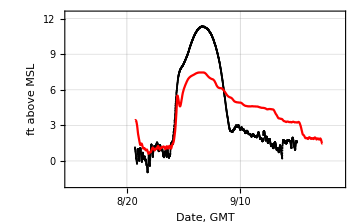
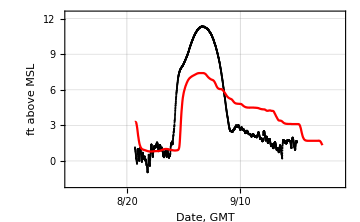
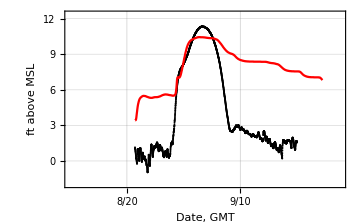
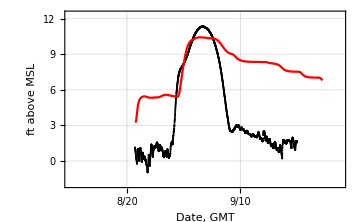
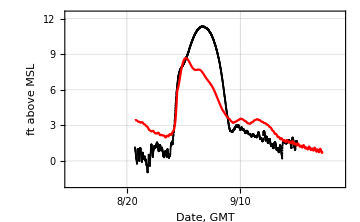
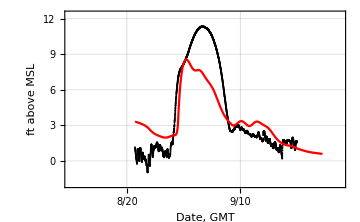
```mathematica
({{□, □, □, □}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}})
```

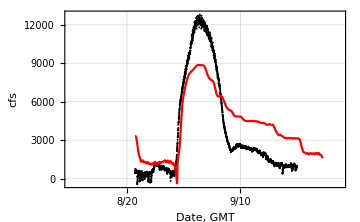
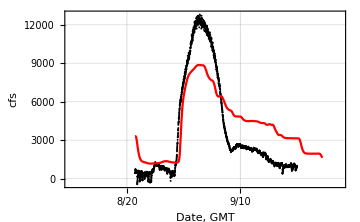
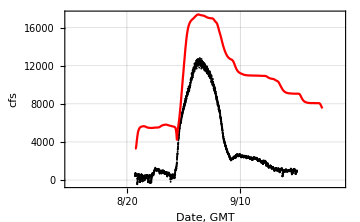
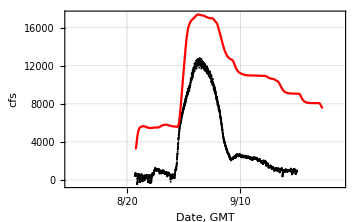
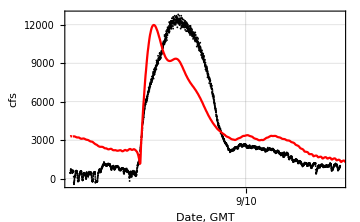
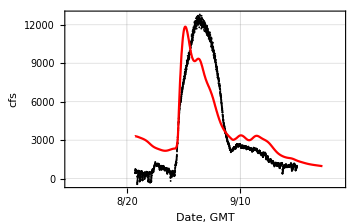
```mathematica
({{□, □, □, □}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}})
```

# Rock Springs

```mathematica
sitename="rock_springs";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```

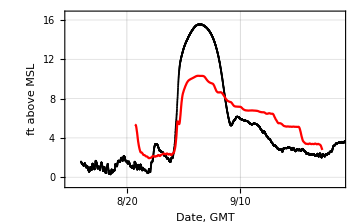
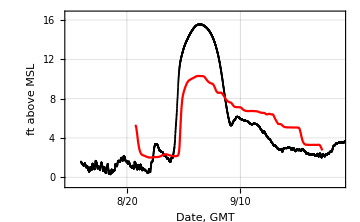
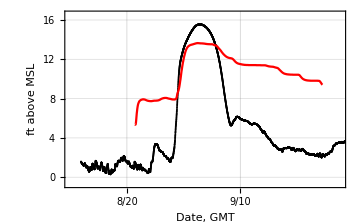
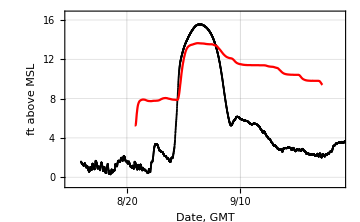
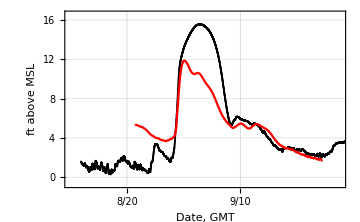
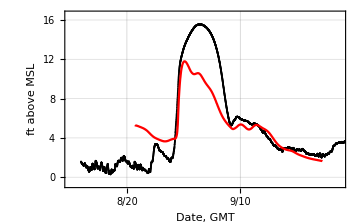
```mathematica
({{□, □, □, □}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}})
```

# Grimesland

```mathematica
sitename="grimesland";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```

Part::partw: Part 3 of {{"40775", "40775.04", "40775.08", "40775.13", "40775.17", "40775.21", "40775.25", "40775.29", "40775.33", "40775.38", "40775.42", "40775.46", "40775.5", "40775.54", "40775.58", "40775.63", "40775.67", "40775.71", "40775.75", "40775.79", "40775.83", "40775.87", "40775.92", "40775.96", "40776", "4" … "4", "4" … "08", "40776.12", "40776.17", "40776.21", "40776.25", "40776.29", "40776.33", "40776.37", "40776.42", "40776.46", "40776.5", "40776.54", "40776.58", "40776.62", "40776.67", "40776.71", "40776.75", "40776.79", "40776.83", "40776.87", "40776.92", "40776.96", "40777", "40777.04", « 15790 »}, « 1 »} does not exist.

ToExpression::notstrbox: {{"40775", "40775.04", "40775.08", "40775.13", "40775.17", "40775.21", "40775.25", "40775.29", "40775.33", "40775.38", "40775.42", "40775.46", "40775.5", "40775.54", "40775.58", "40775.63", "40775.67", "40775.71", "40775.75", "40775.79", "40775.83", "40775.87", "40775.92", "40775.96", "40776", "4" … "4", "" … "", "40776.12", "40776.17", "40776.21", "40776.25", "40776.29", "40776.33", "40776.37", "40776.42", "40776.46", "40776.5", "40776.54", "40776.58", "40776.62", "40776.67", "40776.71", "40776.75", "40776.79", "40776.83", "40776.87", "40776.92", "40776.96", "40777", "40777.04", « 15790 »}, « 1 »} ⟦ 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

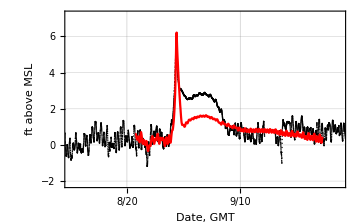
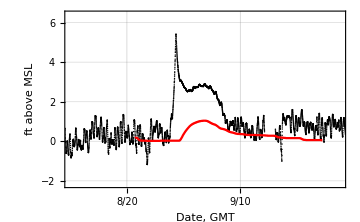
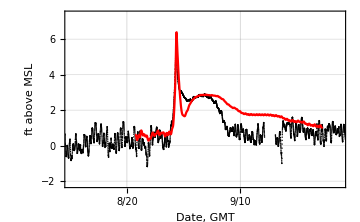
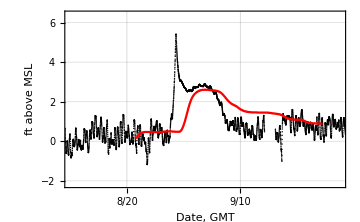
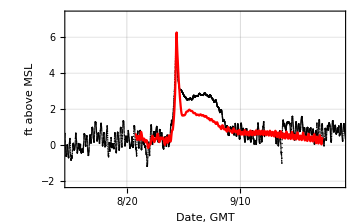
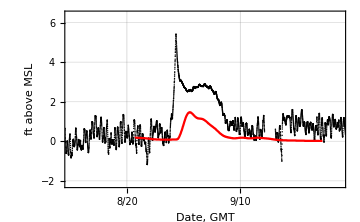
```mathematica
({{□, □, □, □}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}})
```

## Pamlico at Washington

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-1.14, na], Max[29.24, 1 + na]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[0.25, na], Max[29.24, 1 + na]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot :: prng will be suppressed during this calculation.

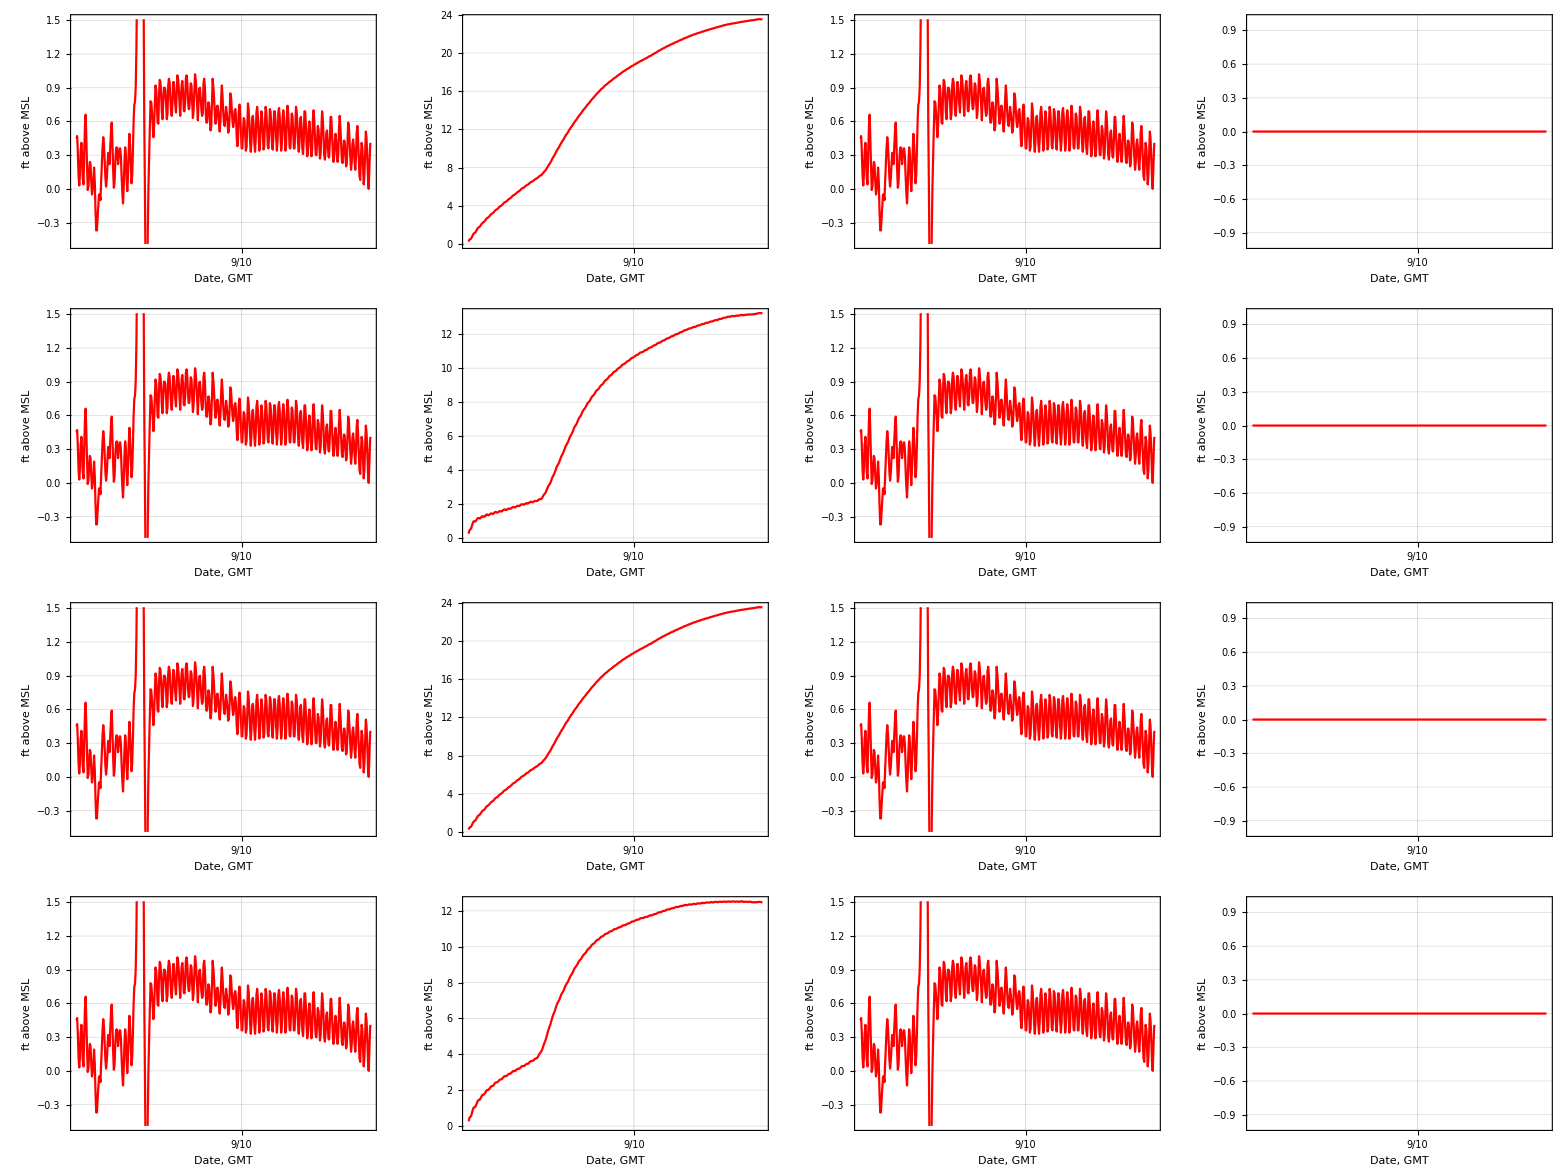
(-Graphics-)

```mathematica
sitename="24100";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[1.×10^-7, na], Max[29.24, 1 + na]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

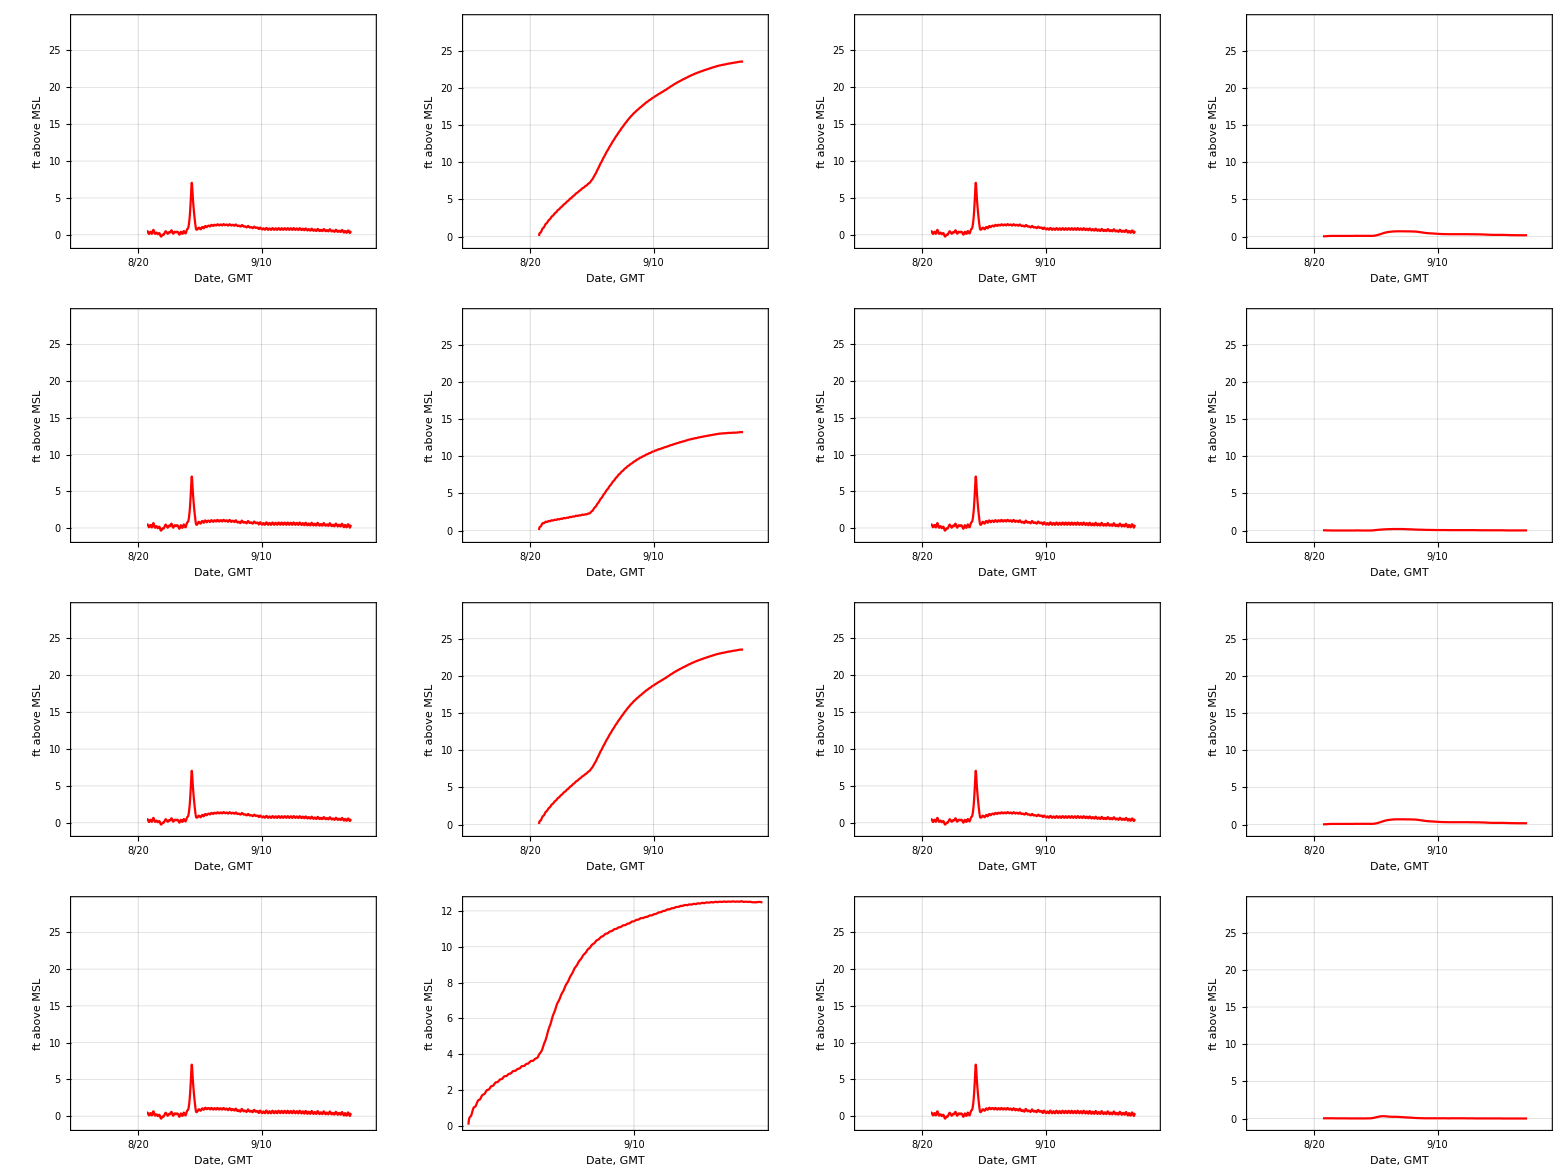
(-Graphics-)

```mathematica
sitename="25100";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[1.×10^-7, na], Max[29.24, 1 + na]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

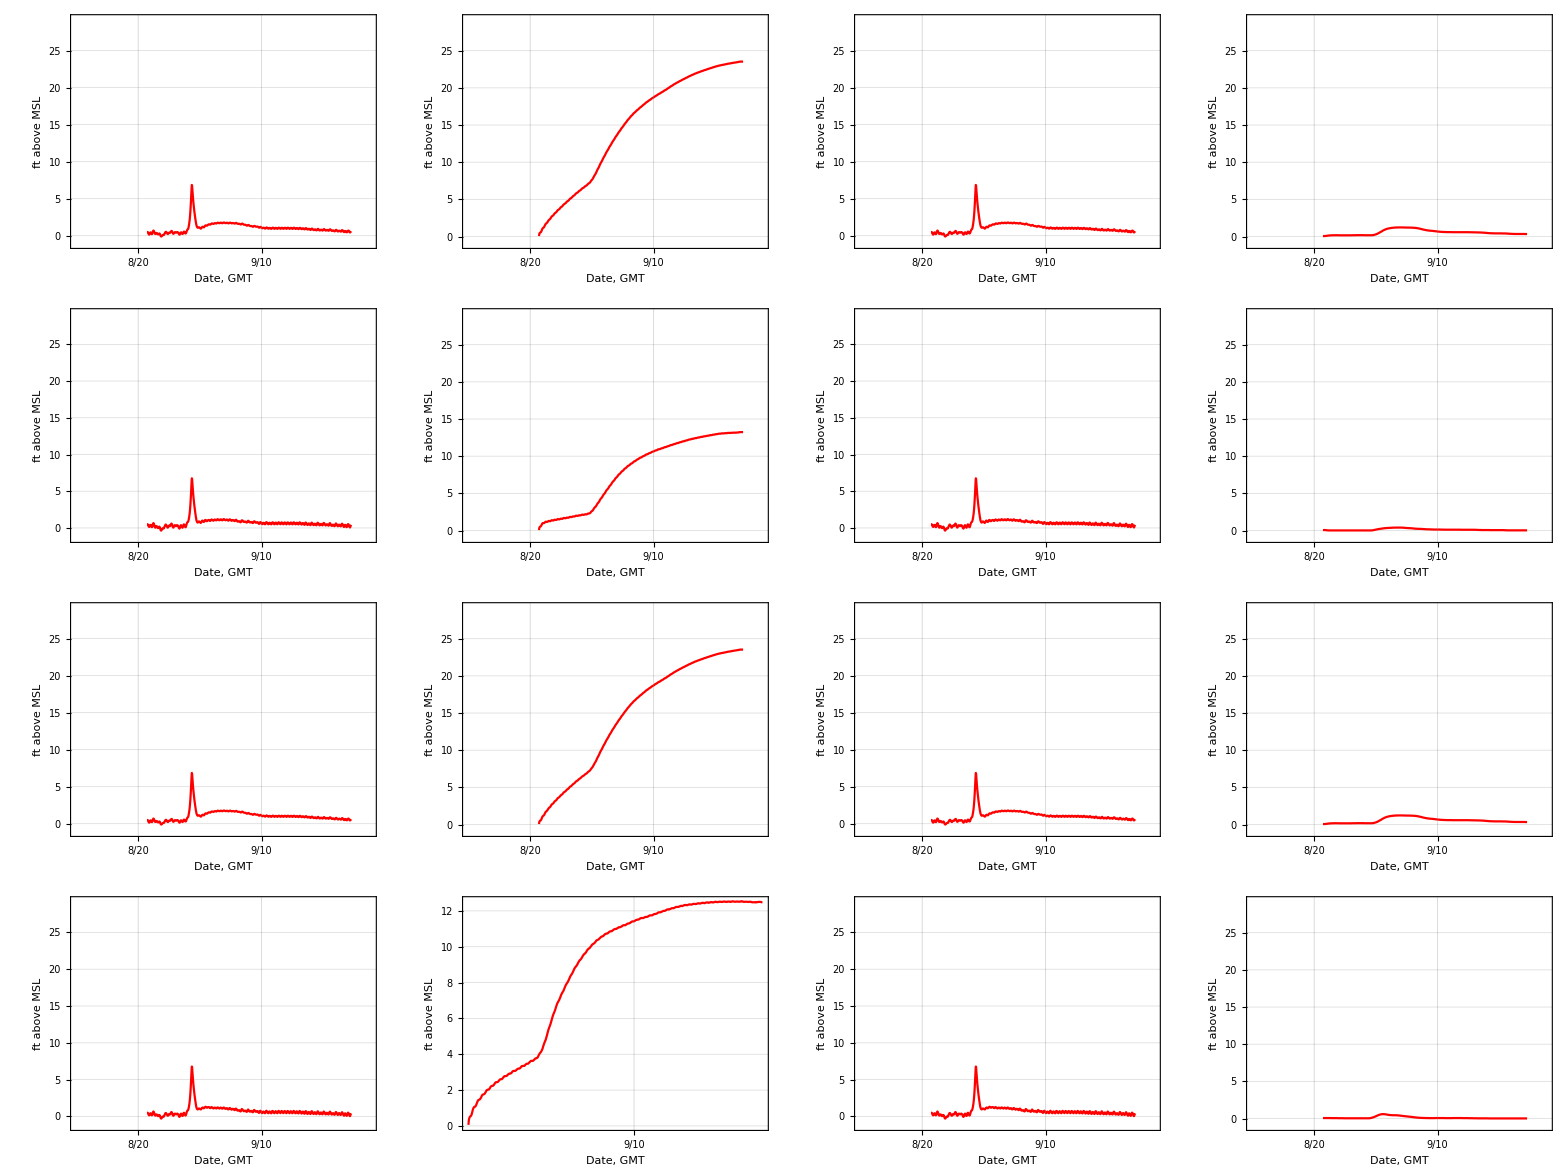
(-Graphics-)

```mathematica
sitename="26100";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```